# Adaptive Recovery

## Step by Step

```mathematica
$Assumptions={0<p<1};
```

```mathematica
RandomDM[d_Integer]:=Module[{psi,rho},
psi=RandomVariate[NormalDistribution[],{d}];
psi=psi/Norm[psi];
rho=Outer[Times,psi,Conjugate[psi]];
rhoFullRank=0.75rho+0.25*IdentityMatrix[2]/2
]

ρ0=RandomDM[2];
ρ0//MatrixForm
Print["Eigenvalues: ", Eigenvalues[ρ0]]
Print["Trace: ", ρ0//Tr]
Print["Purity: ", Tr[ρ0.ρ0]]
```

(0.210852 | -0.238786
-0.238786 | 0.789148)

Eigenvalues: {0.875,0.125}

Trace: 1.

Purity: 0.78125

### Helper Functions

```mathematica
(*Helper Functions*)
Vectorize[rho_]:=Flatten[Transpose[rho]]
UnVectorize[rho_]:=Module[{rowVec},
rowVec=Flatten[rho];
Transpose[Partition[rowVec,Sqrt[Length[rowVec]]]]
]
ApplyKraus[kraus_,rho_]:=Module[{Nkraus},
Sum[k.rho.ConjugateTranspose[k],{k,kraus}]
]
ApplyMap[M_,rho_]:=Module[{},
UnVectorize[M.Vectorize[rho]]
];
(*Checks if||m1-m2|| <tolerance*)
IsMatrixClose[m1_,m2_,tol_:10^-6]:=Norm[m1-m2]<tol
(*2. Compute Quantum Fidelity F=(Tr|sqrt(rho).sigma.sqrt(rho)|)^2*)
Fidelity[rho_,sigma_]:=Module[{r,s,prod,traceVal},
r=Chop[rho];
s=Chop[sigma];
prod=MatrixPower[r,1/2].s.MatrixPower[r,1/2];
traceVal=Tr[MatrixPower[prod,1/2]];
Abs[traceVal]^2
];
```

## 1. Define Noise Kraus Operators and Liouville Matrices

```mathematica
KrausToLiouville[kraus_]:=FullSimplify[
Sum[KroneckerProduct[k,Conjugate[k]],{k,kraus}]
]
```

```mathematica
(*Bitflip Channel*)
BitflipKraus[p_]:=Module[{k0,k1},
k0=Sqrt[1-p] {{1 ,0},{0,1}};
k1=Sqrt[p] {{0, 1},{1,0}};
{k0,k1}
]

(*Dephasing Channel*)
DephasingKraus[p_]:=Module[{k0,k1},
k0=Sqrt[1-p] {{1 ,0},{0,1}};
k1=Sqrt[p] {{1, 0},{0,-1}};
{k0,k1}
]

(*Amplitude Damping Channel*)
AmplitudeDampingKraus[p_]:=Module[{k0,k1},
k0={{1,0},{0,Sqrt[1-p]}};
k1={{0,Sqrt[p]},{0,0}};
{k0,k1}
]

(*Phase Damping Channel (T2)*)
PhaseDampingKraus[p_]:=Module[{k0,k1},
k0={{1,0},{0,Sqrt[1-p]}};
k1={{0,0},{0,Sqrt[p]}};
{k0,k1}
]

(*3. Depolarizing Channel*)
DepolarizingKraus[p_]:=Module[{k0,k1,k2,k3,f},f=Sqrt[p/3];
k0=Sqrt[1-p]*IdentityMatrix[2];
k1=f*PauliMatrix[1];k2=f*PauliMatrix[2];k3=f*PauliMatrix[3];{k0,k1,k2,k3}
]
```

```mathematica
bitflipKraus=BitflipKraus[p];
bitflipLiouville=KrausToLiouville[bitflipKraus];
MatrixForm/@bitflipKraus
bitflipLiouville//MatrixForm
```

{(√(1-p) | 0
0 | √(1-p)),(0 | √p
√p | 0)}

(1-p | 0 | 0 | p
0 | 1-p | p | 0
0 | p | 1-p | 0
p | 0 | 0 | 1-p)

```mathematica
dephasingKraus=DephasingKraus[p];
dephasingLiouville=KrausToLiouville[dephasingKraus];
MatrixForm/@dephasingKraus
dephasingLiouville//MatrixForm
```

{(√(1-p) | 0
0 | √(1-p)),(√p | 0
0 | -√p)}

(1 | 0 | 0 | 0
0 | 1-2 p | 0 | 0
0 | 0 | 1-2 p | 0
0 | 0 | 0 | 1)

```mathematica
(*Try the equivalence between evolutions*)
ApplyKraus[dephasingKraus,ρ0]//MatrixForm
Print["Trace = ", Tr[ApplyKraus[dephasingKraus,ρ0]]]
ApplyMap[dephasingLiouville,ρ0]//MatrixForm
```

(0.210852 | -0.0477572
-0.0477572 | 0.789148)

Trace = 1.

(0.210852 | -0.0477572
-0.0477572 | 0.789148)

## 2. Find the Petz Kraus Operators

Given some noise , the Petz Map  for the state   is defined as:  
 .
This can be defined by its own set of Kraus Operators , starting from the Kraus Operators  of the forward map:

```mathematica
PetzKrausOperators[krausFwd_,sigma_]:=Module[{sigmaOut,invSqrtSigmaOut,sqrtSigma,petzK},
sigmaOut=FullSimplify[Sum[k.sigma.ConjugateTranspose[k],{k,krausFwd}]];
invSqrtSigmaOut=FullSimplify[MatrixPower[sigmaOut,-1/2]];
sqrtSigma=MatrixPower[sigma,1/2];
petzK=Table[sqrtSigma.ConjugateTranspose[k].invSqrtSigmaOut,{k,krausFwd}];
petzK
]
bitflipKrausRec=PetzKrausOperators[bitflipKraus, ρ0];
dephasingKrausRec=PetzKrausOperators[dephasingKraus,ρ0];
```

Now we set the probability p to better handle calculations.

```mathematica
p=0.4;
MatrixForm/@bitflipKrausRec
MatrixForm/@dephasingKrausRec
bitflipLiouvilleRec=KrausToLiouville[bitflipKrausRec];
Print["Bitflip Liouville =   ",bitflipLiouvilleRec//MatrixForm]
dephasingLiouvilleRec=KrausToLiouville[dephasingKrausRec];
Print["Dephasing Liouville = ",dephasingLiouvilleRec//MatrixForm]
```

{(0.485198 | -0.0809623
0.0304901 | 0.93405),(-0.0888556 | 0.344565
0.869343 | 0.0476452)}

{(0.700526 | -0.133649
-0.255449 | 0.747957),(0.592509 | 0.155691
-0.304864 | -0.631236)}

Bitflip Liouville =   (0.243313 | -0.0698993 | -0.0698993 | 0.12528
-0.0624523 | 0.448966 | 0.297077 | -0.059206
-0.0624523 | 0.297077 | 0.448966 | -0.059206
0.756687 | 0.0698993 | 0.0698993 | 0.87472)

Dephasing Liouville = (0.841804 | -0.00137658 | -0.00137658 | 0.0421019
-0.359583 | 0.14995 | -0.013324 | -0.198242
-0.359583 | -0.013324 | 0.14995 | -0.198242
0.158196 | 0.00137658 | 0.00137658 | 0.957898)

Apply Noise to the state and Recover it.
We can recover using Kraus Operators of the Liouville Operator:

```mathematica
Ω1=bitflipLiouville;
P1=bitflipLiouvilleRec;
ρnoisy=ApplyMap[Ω1,ρ0];
(*Using Recovery Kraus Operators*)
ρout=Sum[k.ρnoisy.ConjugateTranspose[k],{k,bitflipKrausRec}];
Print["Fidelity of Kraus Recovery: ", Fidelity[ρ0,ρout]]
(*Using the Liouville Operator*)
ρout=UnVectorize[P1.Vectorize[ρnoisy]];
Print["Fidelity of Liouville Recovery: ", Fidelity[ρ0,ρout]]
Print["Recovered ρ = ", ρout//MatrixForm]
```

Fidelity of Kraus Recovery: 1.

Fidelity of Liouville Recovery: 1.

Recovered ρ = (0.210852 | -0.238786
-0.238786 | 0.789148)

## 4. Try other noises

```mathematica
Clear[p]
```

```mathematica
ampdampKraus=AmplitudeDampingKraus[p];
ampdampLiouville=KrausToLiouville[ampdampKraus];
MatrixForm/@ampdampKraus
ampdampLiouville//MatrixForm
```

{(1 | 0
0 | 0.774597),(0 | 0.632456
0 | 0)}

(1. | 0. | 0. | 0.4
0. | 0.774597 | 0. | 0.
0. | 0. | 0.774597 | 0.
0. | 0. | 0. | 0.6)

```mathematica
phdampKraus=PhaseDampingKraus[p];
phdampLiouville=KrausToLiouville[phdampKraus];
MatrixForm/@phdampKraus
phdampLiouville//MatrixForm
```

{(1 | 0
0 | 0.774597),(0 | 0
0 | 0.632456)}

(1. | 0. | 0. | 0.
0. | 0.774597 | 0. | 0.
0. | 0. | 0.774597 | 0.
0. | 0. | 0. | 1.)

```mathematica
ampdampKrausRec=PetzKrausOperators[ampdampKraus, ρ0];
phdampKrausRec=PetzKrausOperators[phdampKraus,ρ0];
```

```mathematica
Block[{p,ampdampLiouvilleRec,phdampLiouvilleRec},
p=0.1;
Print["Amplitude Damping Recovery Operators:\n",MatrixForm/@ampdampKrausRec];
Print["Phase Damping Recovery Operators:\n",MatrixForm/@phdampKrausRec];
ampdampLiouvilleRec=KrausToLiouville[ampdampKrausRec];
phdampLiouvilleRec=KrausToLiouville[phdampKrausRec];
Print["Bitflip Supermap:\n", MatrixForm[bitflipLiouvilleRec]];
Print["Dephasing Supermap:\n", MatrixForm[dephasingLiouvilleRec]];
Print["Amplitude Damping Supermap:\n", MatrixForm[ampdampLiouvilleRec]];
Print["Phase Damping Supermap:\n", MatrixForm[phdampLiouvilleRec]];
]
```

Amplitude Damping Recovery Operators:
{(0.570377 | -0.100001
-0.0763422 | 0.981811),(-0.170549 | -0.0336568
0.799847 | 0.157845)}

Phase Damping Recovery Operators:
{(0.958096 | -0.00986574
-0.186414 | 0.737345),(-0.0453556 | -0.140856
0.21271 | 0.660594)}

Bitflip Supermap:
(0.243313 | -0.0698993 | -0.0698993 | 0.12528
-0.0624523 | 0.448966 | 0.297077 | -0.059206
-0.0624523 | 0.297077 | 0.448966 | -0.059206
0.756687 | 0.0698993 | 0.0698993 | 0.87472)

Dephasing Supermap:
(0.841804 | -0.00137658 | -0.00137658 | 0.0421019
-0.359583 | 0.14995 | -0.013324 | -0.198242
-0.359583 | -0.013324 | 0.14995 | -0.198242
0.158196 | 0.00137658 | 0.00137658 | 0.957898)

Amplitude Damping Supermap:
(0.354417 | -0.051298 | -0.051298 | 0.0111329
-0.179957 | 0.533082 | -0.019286 | -0.103494
-0.179957 | -0.019286 | 0.533082 | -0.103494
0.645583 | 0.051298 | 0.051298 | 0.988867)

Phase Damping Supermap:
(0.920004 | -0.00306369 | -0.00306369 | 0.0199379
-0.18825 | 0.676486 | -0.0281225 | -0.100323
-0.18825 | -0.0281225 | 0.676486 | -0.100323
0.0799956 | 0.00306369 | 0.00306369 | 0.980062)

## 5. Long term behaviour of the maps

We want to check that after some number of steps the Petz maps converges to one replacement channel.
No matter the map chosen to recover from, the final supermap will be the Identity.
We do this in two parts:
 	1. Choose two possible noises  and . Choose one “noise history” with fixed noise , , where  are random recoveries of the preceeding noise (supposing it is always  or ).
 	2. Choose two possible noises  and . Choose one “noise history” with fixed noise , , where  is always the wrong recovery.

```mathematica
(*Function to compute the Petz Recovery Map Superoperator*)PetzMapSuperoperator[S_?MatrixQ,sigma_?MatrixQ]:=Module[{dim,sigmaVec,NsigmaVec,Nsigma,NsigmaInvHalf,sigmaHalf,preMult,postMult,SAdjoint},(*1. Deduce the Hilbert space dimension from the superoperator S*)
dim=Sqrt[Length[S]];
(*2. Evolve the reference state sigma through the channel*)
sigmaVec=Flatten[sigma];
NsigmaVec=S.sigmaVec;
Nsigma=Partition[NsigmaVec,dim];
(*3. Calculate the necessary matrix powers*)(*Note:We use PseudoInverse on the square root to safely handle cases where N(sigma) might be rank-deficient.*)NsigmaInvHalf=PseudoInverse[MatrixPower[Nsigma,1/2]];
sigmaHalf=MatrixPower[sigma,1/2];
(*4. Construct the pre-and post-multiplication superoperators*)
(*Rule:A ρ B is represented by A⊗B^T*)
preMult=KroneckerProduct[NsigmaInvHalf,Transpose[NsigmaInvHalf]];
postMult=KroneckerProduct[sigmaHalf,Transpose[sigmaHalf]];
(*5. Adjoint of the channel's superoperator*)
SAdjoint=ConjugateTranspose[S];
(*6. Combine everything via matrix multiplication*)
postMult.SAdjoint.preMult
]
```

```mathematica
Ω1=ampdampLiouville;
P1Kraus=ampdampKrausRec;
P1Liouville=KrausToLiouville[P1Kraus];
P1Liouville2=PetzMapSuperoperator[Ω1,ρ0];
Print["Are recovery maps equal? ", P1Liouville==P1Liouville2];
ρnoisy=ApplyMap[Ω1,ρ0];
(*Using Recovery Kraus Operators*)
ρout=ApplyKraus[P1Kraus,ρnoisy];
Print["Fidelity of Kraus Recovery: ", Fidelity[ρ0,ρout]]
(*Using the Liouville Operator*)
ρout=ApplyMap[P1Liouville,ρnoisy];
Print["Fidelity of Liouville Recovery: ", Fidelity[ρ0,ρout]]
(*Using the direct Liouville Operator*)
ρout=ApplyMap[P1Liouville2,ρnoisy];
Print["Fidelity of Liouville Recovery: ", Fidelity[ρ0,ρout]]
Print["Recovered ρ = ", ρout//MatrixForm]
```

Are recovery maps equal? True

Fidelity of Kraus Recovery: 1.

Fidelity of Liouville Recovery: 1.

Fidelity of Liouville Recovery: 1.

Recovered ρ = (0.210852 | -0.238786
-0.238786 | 0.789148)

```mathematica
Ωa=KrausToLiouville[AmplitudeDampingKraus[0.1]];
Ωb=KrausToLiouville[PhaseDampingKraus[0.1]];
(* Recover the Phase Damping [WRONG] *)
P1=PetzMapSuperoperator[Ωb,ρ0];
(* Update the noises *)
Na=Ωa.P1.Ωa;
Nb=Ωb.P1.Ωb;
(* Check that it is truly recovering the Phase Damping Noise *)
Print["1. Recover Nb:\n",
"F(ρ0,P1(Nb)×Ωa×ρ0) = ",Fidelity[ρ0,UnVectorize[P1.Ωa.Vectorize[ρ0]]],
"\n",
"F(ρ0,P1(Nb)×Ωb×ρ0) = ",Fidelity[ρ0,UnVectorize[P1.Ωb.Vectorize[ρ0]]]
]
```

1. Recover Nb:
F(ρ0,P1(Nb)×Ωa×ρ0) = 0.991355
F(ρ0,P1(Nb)×Ωb×ρ0) = 1.

1. Recover Nb:
F(ρ0,P1(Nb)×Ωa×ρ0) = 0.991355\nF(ρ0,P1(Nb)×Ωb×ρ0) = 1.

```mathematica
(* Recover the Phase Damping [WRONG] *)
Print["  2. Recover Nb:"]
P2=PetzMapSuperoperator[Nb,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P2(Nb)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P2.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P2(Nb)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P2.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P2.Na;
Nb=Ωb.P2.Nb;
(* Recover the Phase Damping [WRONG] *)
Print["  3. Recover Nb:"]
P3=PetzMapSuperoperator[Nb,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P3(Nb)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P3.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P3(Nb)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P3.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P3.Na;
Nb=Ωb.P3.Nb;
(* Recover the Amplitude Damping [RIGHT] *)
Print["  4. Recover Na:"]
P4=PetzMapSuperoperator[Na,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P4(Na)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P4.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P4(Na)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P4.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P4.Na;
Nb=Ωb.P4.Nb;
(* Recover the Amplitude Damping [RIGHT] *)
Print["  5. Recover Na:"]
P5=PetzMapSuperoperator[Na,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P5(Na)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P5.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P5(Na)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P5.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P5.Na;
Nb=Ωb.P5.Nb;
(* Recover the Phase Damping [WRONG] *)
Print["  6. Recover Nb:"]
P6=PetzMapSuperoperator[Nb,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P6(Nb)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P6.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P6(Nb)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P6.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P6.Na;
Nb=Ωb.P6.Nb;
(* Recover the Amplitude Damping [RIGHT] *)
Print["  7. Recover Na:"]
P7=PetzMapSuperoperator[Na,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P7(Na)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P7.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P7(Na)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P7.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P7.Na;
Nb=Ωb.P7.Nb;
(* Recover the Amplitude Damping [RIGHT] *)
Print["  8. Recover Na:"]
P8=PetzMapSuperoperator[Na,ρ0];
(* Check that it is truly recovering the Phase Damping Noise *)
Print[
"F(ρ0,P8(Na)×Na×ρ0) = ",Fidelity[ρ0,UnVectorize[P8.Na.Vectorize[ρ0]]],
"\n",
"F(ρ0,P8(Na)×Nb×ρ0) = ",Fidelity[ρ0,UnVectorize[P8.Nb.Vectorize[ρ0]]]
]
(* Update noises *)
Na=Ωa.P8.Na;
Nb=Ωb.P8.Nb;
```

2. Recover Nb:

F(ρ0,P2(Nb)×Na×ρ0) = 0.974405
F(ρ0,P2(Nb)×Nb×ρ0) = 1.

3. Recover Nb:

F(ρ0,P3(Nb)×Na×ρ0) = 0.959233
F(ρ0,P3(Nb)×Nb×ρ0) = 1.

4. Recover Na:

F(ρ0,P4(Na)×Na×ρ0) = 1.
F(ρ0,P4(Na)×Nb×ρ0) = 0.987108

5. Recover Na:

F(ρ0,P5(Na)×Na×ρ0) = 1.
F(ρ0,P5(Na)×Nb×ρ0) = 0.999329

6. Recover Nb:

F(ρ0,P6(Nb)×Na×ρ0) = 0.999976
F(ρ0,P6(Nb)×Nb×ρ0) = 1.

7. Recover Na:

F(ρ0,P7(Na)×Na×ρ0) = 1.
F(ρ0,P7(Na)×Nb×ρ0) = 1.

8. Recover Na:

F(ρ0,P8(Na)×Na×ρ0) = 1.
F(ρ0,P8(Na)×Nb×ρ0) = 1.

```mathematica
(* Final recovery possibilities *)
P9a=PetzMapSuperoperator[Na,ρ0];
P9b=PetzMapSuperoperator[Nb,ρ0];
P9a//MatrixForm
P9b//MatrixForm
P9a.Na//MatrixForm
P9b.Na//MatrixForm
P9b.Nb//MatrixForm
```

(0.210852 | -4.10993×10^-14 | -4.14987×10^-14 | 0.210852
-0.238786 | 2.1761×10^-14 | 2.22219×10^-14 | -0.238786
-0.238786 | 2.17459×10^-14 | 2.22484×10^-14 | -0.238786
0.789148 | 4.21678×10^-14 | 4.06641×10^-14 | 0.789148)

(0.210852 | -8.11243×10^-14 | -8.14387×10^-14 | 0.210852
-0.238786 | 3.3914×10^-14 | 3.42962×10^-14 | -0.238786
-0.238786 | 3.39015×10^-14 | 3.43114×10^-14 | -0.238786
0.789148 | 8.16818×10^-14 | 8.04479×10^-14 | 0.789148)

(0.210852 | -2.30667×10^-17 | -1.9569×10^-16 | 0.210852
-0.238786 | 2.61225×10^-17 | 2.21615×10^-16 | -0.238786
-0.238786 | 2.61225×10^-17 | 2.21615×10^-16 | -0.238786
0.789148 | -8.63305×10^-17 | -7.32401×10^-16 | 0.789148)

(0.210852 | -2.30667×10^-17 | -1.9569×10^-16 | 0.210852
-0.238786 | 2.61225×10^-17 | 2.21615×10^-16 | -0.238786
-0.238786 | 2.61225×10^-17 | 2.21615×10^-16 | -0.238786
0.789148 | -8.63305×10^-17 | -7.32401×10^-16 | 0.789148)

(0.210852 | -2.35915×10^-17 | -1.97838×10^-16 | 0.210852
-0.238786 | 2.67169×10^-17 | 2.24048×10^-16 | -0.238786
-0.238786 | 2.67169×10^-17 | 2.24048×10^-16 | -0.238786
0.789148 | -8.82948×10^-17 | -7.4044×10^-16 | 0.789148)

```mathematica
MatrixForm/@{P1,P2,P3,P4,P5,P6,P7,P8}
```

{(0.977366 | -0.00114903 | -0.00114903 | 0.00538796
-0.0544666 | 0.914671 | -0.0102108 | -0.0284004
-0.0544666 | -0.0102108 | 0.914671 | -0.0284004
0.0226342 | 0.00114903 | 0.00114903 | 0.994612),(0.955485 | -0.00210275 | -0.00210275 | 0.0106869
-0.100612 | 0.793819 | -0.0176905 | -0.0529097
-0.100612 | -0.0176905 | 0.793819 | -0.0529097
0.0445154 | 0.00210275 | 0.00210275 | 0.989313),(0.913828 | -0.00353493 | -0.00353493 | 0.0209949
-0.172568 | 0.598209 | -0.0265445 | -0.0923769
-0.172568 | -0.0265445 | 0.598209 | -0.0923769
0.0861721 | 0.00353493 | 0.00353493 | 0.979005),(0.367146 | -0.0469973 | -0.0469973 | 0.0382594
-0.212414 | 0.273439 | -0.0169274 | -0.14486
-0.212414 | -0.0169274 | 0.273439 | -0.14486
0.632854 | 0.0469973 | 0.0469973 | 0.961741),(0.290146 | -0.0192409 | -0.0192409 | 0.166227
-0.252758 | 0.0784368 | -0.00959848 | -0.211129
-0.252758 | -0.00959848 | 0.0784368 | -0.211129
0.709854 | 0.0192409 | 0.0192409 | 0.833773),(0.240942 | -0.00434897 | -0.00434897 | 0.201438
-0.249529 | 0.00781283 | -0.00105962 | -0.234439
-0.249529 | -0.00105962 | 0.00781283 | -0.234439
0.759058 | 0.00434897 | 0.00434897 | 0.798562),(0.211235 | -0.000108771 | -0.000108771 | 0.210624
-0.238986 | 0.0000921508 | 0.0000304297 | -0.238663
-0.238986 | 0.0000304297 | 0.0000921508 | -0.238663
0.788765 | 0.000108771 | 0.000108771 | 0.789376),(0.210853 | -9.34583×10^-8 | -9.34583×10^-8 | 0.210852
-0.238786 | 5.16427×10^-8 | 4.8019×10^-8 | -0.238786
-0.238786 | 4.8019×10^-8 | 5.16427×10^-8 | -0.238786
0.789147 | 9.34583×10^-8 | 9.34583×10^-8 | 0.789148)}

### Note

The maps are becoming more and more a Pin Map, with the first and last columns equal to the vectorized state to recover ρ0 and other columns null. Whatever is the input , .
We can see this plotting the differences between the rows of the Petz maps implemented and the vectorized ρ0.

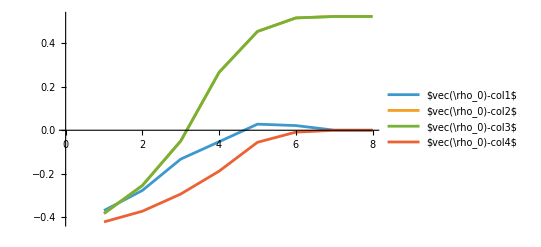

```mathematica
maps={P1,P2,P3,P4,P5,P6,P7,P8};
ListLinePlot[Module[
{data},
data=Table[Total[Vectorize[ρ0]-#]&/@map,{map,Transpose/@maps}];
Transpose[data]],
PlotLegends->{"$vec(\rho_0)-col1$","$vec(\rho_0)-col2$","$vec(\rho_0)-col3$","$vec(\rho_0)-col4$"}
]
```